拟合得到的函数是：-52.2-0.88 x

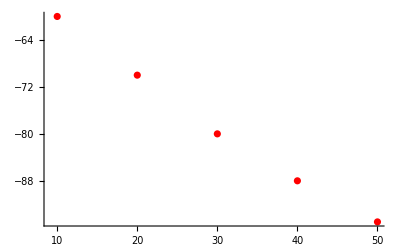

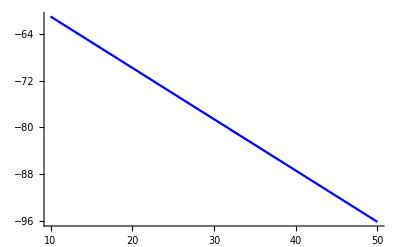

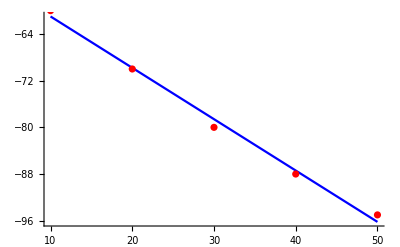

```mathematica
(*假设我们有一组实验数据*)data={{10,-60},{20,-70},{30,-80},{40,-88},{50,-95}};

(*使用 Fit 命令进行线性拟合*)
(*假设信号强度与距离的对数成线性关系*)
fit=Fit[data,{1,x},x];

(*显示拟合结果*)
Print["拟合得到的函数是：",fit];

(*绘制原始数据和拟合曲线*)
ListPlot[data,PlotStyle->Red]
Plot[fit,{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Blue]
Show[%,%%]
```